```mathematica
-
```

```mathematica
(*Want to find the onsite interaction of the system. Remember, we want to build an effective bose-hubbard hamiltonian.*)
```

```mathematica
(*First, define and test a wannier function function. Find the vectors first, as that will save dramatic amounts of time. *)
```

```mathematica
(*Wannier Process 1D*)

(*1. Find eigenvectors L=12, c=.5,V=10, b=2, p=45*)
L=12;
c=.5;
V=10;
b=2;
p=45;
WE = computePlaneMatrix2Well[V,c,b,L,p];
(* WE[[1]]+10000*)
groundState1D[WE[[2]][[1]],12,x];
(*Now, take the eigenvectors, and build the wannier functions*)
WigPsi0 [x_] = groundState1D[WE[[2]][[1]],12,x];
WigPsi1[x_] = groundState1D[WE[[2]][[2]],12,x];
(*Check normalization of the ground and excite state*)
Wig1 [x_] :=Wig1[x]=(Re[WigPsi0[x]]+Im[WigPsi1[x]])/Sqrt[2];
Wig2 [x_] :=Wig2[x]=(Re[WigPsi0[x]]-Im[WigPsi1[x]])/Sqrt[2];
```

```mathematica
a
```

```mathematica
(*Plot[Wig1[x],{x,-5,5}];NIntegrate[Abs[WigPsi1[x]]^2,{x,-6,6}];
Plot[{Wig1[x],Re[Wig2[x]]},{x,-5,5},PlotRange-> All];*)
```

```mathematica
(*Now, calculate the onsite interaction*)
```

-0.000027491

```mathematica
U1 =NIntegrate[Wig1[x]^2,{x,-L/2,L/2}]
```

1.

```mathematica
U2 = NIntegrate[Wig2[x]^4,{x,-L/2,L/2}]
```

0.888539

```mathematica
(*Calculate the tunneling rates*)
```

```mathematica
J = WE[[1]][[2]]-WE[[1]][[1]]
```

0.0000637181

```mathematica
LatticeVector = b
```

2

```mathematica
(*Calculate the Raman assisted tunneling rates. Come back to this later.*)
(*LatticeVector = b (site of well*)
LatticeVector =b
K =Manipulate[ NIntegrate[Conjugate[Wig1[x]]*Wig2[x]*Exp[ⅈ*(2*π/12*y*(x+LatticeVector))],{x,-L/2,L/2}],{y,.1,L}]
```

2.

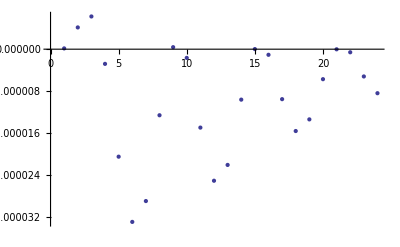

```mathematica
KPlotR = ListPlot[Table[Re[NIntegrate[Conjugate[Wig1[x]]*Wig2[x]*Exp[ⅈ*(2*π/12*y*(x+LatticeVector))],{x,-L/2,L/2}]],{y,.1,L,.5}]]
```

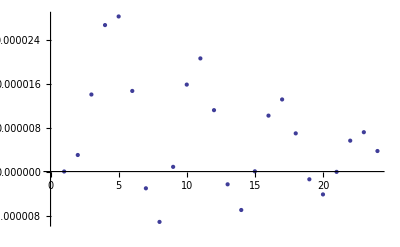

```mathematica
KPlotI = ListPlot[Table[Im[NIntegrate[Conjugate[Wig1[x]]*Wig2[x]*Exp[ⅈ*(2*π/12*y*(x+LatticeVector))],{x,-L/2,L/2}]],{y,.1,L,.5}]]
```

```mathematica
Wig2[2]
```

1.13199

```mathematica
L
```

12

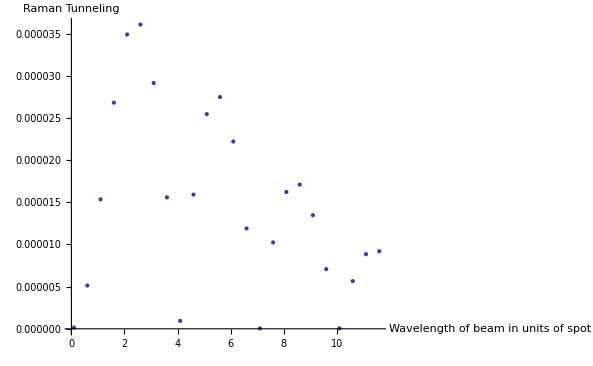

```mathematica
KPlotAbs= ListPlot[Table[{y,Abs[NIntegrate[Conjugate[Wig1[x]]*Wig2[x]*Exp[ⅈ*(2*π/12*y*(x+LatticeVector))],{x,-L/2,L/2}]]},{y,.1,L,.5}],AxesLabel->{"Wavelength of beam in units of spot size","Raman Tunneling"}]
```

```mathematica
(*Now, plot the onsite vs the tunneling vs the raman tunneling*)
```

```mathematica
(*This functionality is now in function WigMaker, which will create the wigner functions for a given set of specs*)
 (*{W0,W1,EW} = WigMaker[10,.5,2,12,45]*)
U1 =NIntegrate[Wig1[x]^2,{x,-L/2,L/2}]
UList = Table[{b,Onsite[10,.5,b,12,45]},{b,0,2,.1}]
```

1.

{{0.,1.1803},{0.1,1.16561},{0.2,1.12293},{0.3,1.05691},{0.4,0.976523},{0.5,0.896261},{0.6,0.83617},{0.7,0.815541},{0.8,0.832255},{0.9,0.85818},{1.,0.875195},{1.1,0.883346},{1.2,0.886693},{1.3,0.887932},{1.4,0.888353},{1.5,0.888486},{1.6,0.888525},{1.7,0.888536},{1.8,0.888538},{1.9,0.888539},{2.,0.888539}}

```mathematica
ListPlot[{UList,JList},PlotLegends->{"Onsite","Tunneling"},PlotRange->All]
```

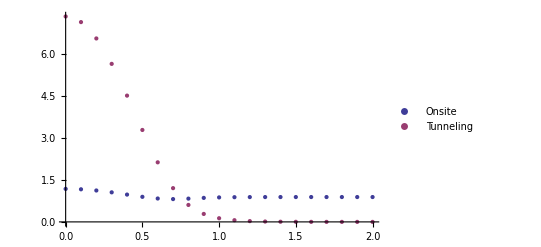

```mathematica
EList = Table[{b,WigMaker[10,.5,b,12,45][[3]]},{b,0,2,.1}]
```

```mathematica
JList = Table[{EList[[p]][[1]],EList[[p]][[2]][[2]]-EList[[p]][[2]][[1]]},{p,1,Length[EList]}]
```

{{0.,7.34419},{0.1,7.14269},{0.2,6.55807},{0.3,5.64945},{0.4,4.51427},{0.5,3.28653},{0.6,2.12954},{0.7,1.20642},{0.8,0.606203},{0.9,0.284652},{1.,0.131098},{1.1,0.0604756},{1.2,0.028053},{1.3,0.0130679},{1.4,0.0061021},{1.5,0.00285206},{1.6,0.00133398},{1.7,0.000623979},{1.8,0.000291667},{1.9,0.000136732},{2.,0.0000637181}}

```mathematica
(*Want to test out the tunneling rates*)
W = WigMaker[10,.5,0,12,45];
W0 = W[[1]];
W1 = W[[2]];
```

```mathematica
W[[3]]+10000
```

{-15.9053,-8.56114,-3.08374}

```mathematica
Manipulate[ListPlot[Table[{x,WigMaker[V,.5,b,12,20][[1]][x]},{x,-6,6,.1}]],{V,0,10},{b,0,3}]
```

```mathematica
WigMaker[10,.5,.3,12,20][[1]][x]//N
```

```mathematica
Manipulate[ListPlot[{ Table[{x,Re[groundState1Dplt[V,.5,b,12,20][[1]][x]]},{x,-6,6,.2}],Table[{x,Im[groundState1Dplt[V,.5,b,12,20][[2]][x]]},{x,-6,6,.5}]},PlotLegends->{"Ground","1E"}],{V,0,10},{b,0,3}]
```

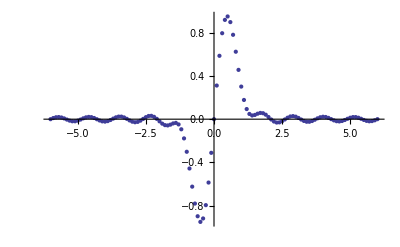

```mathematica
ListPlot[Table[{x,Im[groundState1Dplt[10,.5,.2,12,20][[2]][x]]},{x,-6,6,.1}],PlotRange->All]
```

## Functions:

```mathematica
Ψ[n_,x_,m_,y_,L_]:= 1/L*Exp[-ⅈ*2 π/L(n*x+y*m)]
```

```mathematica
Hp[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
H2p[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x+b)^2+y^2))/c^2]Φ[n,x,m,y,L]-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
HPlane[V_,L_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[(-(2*π/L)^2(n-l)^2)/8]*π*1/(2*L^2)Exp[(-(2*π/L)^2(m-q)^2)/8]
```

```mathematica
HPlanebtest[V_,L_,n_,m_,l_,q_,b_]:= 
(*I had some trouble getting the factors in EXp right, but this configuration worked. This is for one well only! This is the generalizating of HPlane, which doesn't worry about b. This basically lets me offset my one well wherever I want to double check that I have the right form of the analytics*)KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ(2*π/L)(m-q))^2/8]
```

```mathematica
H2Plane[V_,L_,b_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]-V*Exp[((-2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]//N
```

```mathematica
HMatrix[V_,L_,size_]:=ArrayFlatten[Table[HPlane[V,L,m,l,n,q],{m,-size,size},{n,-size,size},{l,-size,size},{q,-size,size}]//N]
```

```mathematica
groundState[EM_,L_,x_,y_]:=Compile[{Size=Sqrt[Length[EM]], i,j},
(*Given an eigenvector, this will compute a plottable version of the wavefunction. However, there is little sophistication, the user must still change the index conversion number by hand.

Note: there was a problem: use ky for calculating the number on x and y, as the kx function gives the row of a matrix, but, for the eigenvector, it is just a 'column' vector, so just use ky*) Sum[Normalize[EM][[(i-1)*Size+j]]*N[Exp[-ⅈ*2.*π/L*(ky[i,Size]*x+ky[j,Size]*y)]/L,8],{i,1,Size},{j,1,Size}]]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix//N]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

Harmonic Oscillator Functions:
HMV1[1,2,.1,0,.5]

```mathematica
HMV1[1,1,.1,0,0.5]
```

0.0103913

```mathematica
HMV1[1,2,0.1,0.5]
```

HMV1[1,2,0.1,0.5]

```mathematica
HMV1[l_,m_,ω_,b_,c_]:= (Sqrt[ω]/Sqrt[2^(l+m)Factorial[l]*Factorial[m]]*Sum[{2^k Factorial[k]*Binomial[l,k]*Binomial[m,k]*(1-2*(ω*c^2)/(1+2 c^2 ω))^((m+l)/2-k)*HermiteH[(m+l-2*k),Sqrt[ω/(1+2*c^2*ω)]*b]},{k,0,Min[m,l]}]*Exp[b^2/(2 c^2)(1/(1+2 c^2*ω)-1)]*Sqrt[2/(1+2 c^2*ω)]c)[[1]]
```

```mathematica
Hx2Anal2[l_,m_]:= 1/2(2*l+1)*KroneckerDelta[l,m]-1/2 Sqrt[(l+1)(l+2)]KroneckerDelta[l+1,m-1]-1/2 Sqrt[(m+1)(m+2)]KroneckerDelta[l-1,m+1]
```

```mathematica
HOBasis[V_,b_,c_,size_]:= Module[{ω=Sqrt[(2V)/c^2]},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,b,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{l,0,size-1},{m,0,size-1},{q,0,size-1}]]
```

```mathematica
HOBasis1Well[V_,c_,size_]:= Module[{ω=Sqrt[2*V/c^2]},Table[ω/2*Hx2Anal2[n,m]*KroneckerDelta[l,q]+ω/2*Hx2Anal2[l,q]*KroneckerDelta[m,n]-V*HMV1[n,m,ω,0,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{m,0,size-1},{l,0,size-1},{q,0,size-1}]]
```

```mathematica
plotGround[Ψ_,H_,V_,c_,b_,size_,]:= Compile[{x,k,Em,M,HOBasis},

Plot[{Sum[k,{k,Table[Ψ[n,x,V,c]*Normalize[Em[[2]][[1]]][[n+1]], {n,0,size}]}],-V/(c*Sqrt[2π])Exp[-x^2/(4.*V*c^2)]//N},{x,-10,10}]
]
```

```mathematica
plotGround
```

plotGround

```mathematica
plotGround2wellHO2d[Ψ_,V_,b_,c_,size_]:= Module[{k,ω=Sqrt[2*V/(6b*c+9 c^2)],HOBasis,Em},
HOBasis[V,b,c,size,ω]:= Module[{},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,-b,c]*HMV1[l,q,ω,b,c],{n,0,size},{l,0,size},{m,0,size},{q,0,size}]];
Em = Eigensystem[ArrayFlatten[HOBasis[1.5^2,1,.5,7,ω]-1000*IdentityMatrix[42]]]

Plot[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,x,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,17},{j,1,17}]]^2},{x,-3,3}]
]
```

```mathematica
plotGround2wellHO2dT[Ψ_,V_,b_,c_,size_,Em_]:= Module[{k,ω=Sqrt[2*V/c^2],x,y},
Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}];

Plot3D[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}]]^2},{x,-3,3},{y,-3,3}]
]
```

```mathematica
HM2Well[V_,b_,c_,size_]:= Module[{ω=Sqrt[2*V/(6*b*c+9 c^2)]},
Table[ω/2*Hx2Anal2[n,m]-V*HMV1[n,m,ω,b,c]-V*HMV1[n,m,ω,-b,c],{n,0,size},{m,0,size}]
]
```

```mathematica
EnGround2wellHO[V_,b_,c_,size_]:=EnGround2wellHO[V,b,c,size]= Module[{Em,M},

(M=HM2Well[V,b,c,size]-1000*IdentityMatrix[size+1]);
(Em=Eigenvalues[M])
]
```

### Sparse Matrices Stuff:

```mathematica
R[deltaK_,L_]:=R[deltaK]=Exp[(-(2*π/L)^2(deltaK)^2)/8.]//N
```

```mathematica
yIndex[i_,size_] =Mod[i,size,1]
```

Mod[i,size,1]

```mathematica
(*y index will take a number from 1-n, and convert it into a quantum number for ky. This will be an integer starting from -p..p.*)
```

```mathematica
yIndex[2,4]
```

2

```mathematica
ky[i_,size_]=yIndex[i,size]-(size-1)/2-1
```

-1+(1-size)/2+Mod[i,size,1]

```mathematica
(*this will convert our index number to a range that runs over negative numbers so we can get backwards waves*)
```

```mathematica
kx[i_,size_]=xIndex[i,size]-(size-1)/2-1
```

(1-size)/2+(i-Mod[i,size,1])/size

```mathematica
kx[6,5]
```

-1

```mathematica
xIndex[i_,size_]=(i-Mod[i,size,1])/size+1
```

1+(i-Mod[i,size,1])/size

```mathematica
BuildPlaneMatrix[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
Clear[R]
```

```mathematica
BuildPlaneMatrix2D2Well[V_,L_,p_,b_]:= Module[{MDense,MDiag,i,j,M},
(* I am choosing the wells to be on the x-axis, so the y-axis dynamics shouldn't
change. Notice, the R2W contains b information, and will be used for the kx's, while the R doesn't, and can be used for the ky's without loss of generality, because there are two wells, there is another term in our MDense*)
MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->(R2W[kx[j,p]-kx[i,p],L,b]+R2W[kx[j,p]-kx[i,p],L,-b])*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
R2W[deltaK_,L_,b_]:=R2W[deltaK,L,b]=Exp[((2.*b+ⅈ(2.*π/L)(deltaK)/2)^2-4.*b^2)/2.]//N
```

```mathematica
(*Tunneling for a 2D 2Well case*)
Tunneling2DWellListGen[basisnum_]:=
(*Need to double check that L=1 is okay for small b*)Module[{EnergyList,TunnelingList},
EnergyList= Table[{b,Eigenvalues[BuildPlaneMatrix2D2Well[10,8,basisnum,b/2.]-1000.*IdentityMatrix[basisnum^2],2]+1000},{b,.1,4,.2}];

TunnelingList= Table[{EnergyList[[p]][[1]],EnergyList[[p]][[2]][[2]]-EnergyList[[p]][[2]][[1]]},{p,1,Length[EnergyList]}]
]
```

```mathematica
10/25.
```

0.4

```mathematica
(*1D Functions for plane waves*)
```

```mathematica
computePlaneMatrix2Well[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Eigensystem[Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-10000*IdentityMatrix[p+1],3]

]
```

```mathematica
ComputePlaneWave[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M,EM},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag;

EM = Eigensystem[M-10000*IdentityMatrix[p^2],3]
]
```

```mathematica
ky[5,5]
```

2

```mathematica
groundState1D[EM_,L_,x_]:=Module[{Size =Length[EM],i},
EMn = Normalize[EM];
Sum[EMn[[i]]*N[Exp[-ⅈ*2.*π/L*ky[i,Size]*x]/Sqrt[L],8],{i,1,Size}]
]
```

```mathematica
Clear[EMn]
```

```mathematica
groundState1Dplt[V_,c_,b_,L_,p_]:=Module[{WE,x,gstate,estate},
WE = computePlaneMatrix2Well[V,c,b,L,p];
gstate[x_]:=groundState1D[WE[[2]][[1]],L,x];
estate[x_]:=groundState1D[WE[[2]][[2]],L,x];
{gstate,estate}
]
```

```mathematica
WigMaker[V_,c_,b_,L_,p_]:=Module[{WE,WigPsi0,WigPsi1,Wig1,Wig2,x},
WE = computePlaneMatrix2Well[V,c,b,L,p];
(* WE[[1]]+10000*)
groundState1D[WE[[2]][[1]],12,x];
(*Now, take the eigenvectors, and build the wannier functions*)
WigPsi0 [x_] = groundState1D[WE[[2]][[1]],L,x];
WigPsi1[x_] = groundState1D[WE[[2]][[2]],L,x];
(*Check normalization of the ground and excite state*)
Wig1[x_]:=Wig1[x]=(Re[WigPsi0[x]]+Im[WigPsi1[x]])/Sqrt[2];
Wig2[x_]:=Wig2[x]=(Re[WigPsi0[x]]-Im[WigPsi1[x]])/Sqrt[2];
{Wig1,Wig2,WE[[1]]}
]
```

```mathematica
Onsite[V_,c_,b_,L_,p_] := Module[{WE,WigPsi0,WigPsi1,Wig1,Wig2,x,U},
WE = computePlaneMatrix2Well[V,c,b,L,p];
(*WE[[1]]+10000*)
groundState1D[WE[[2]][[1]],12,x];
(*Now, take the eigenvectors, and build the wannier functions*)
WigPsi0 [x_] = groundState1D[WE[[2]][[1]],12,x];
WigPsi1[x_] = groundState1D[WE[[2]][[2]],12,x];
(*Check normalization of the ground and excite state*)
Wig1[x_]=(Re[WigPsi0[x]]+Im[WigPsi1[x]])/Sqrt[2];
Wig2[x_]=(Re[WigPsi0[x]]-Im[WigPsi1[x]])/Sqrt[2];
U =NIntegrate[Wig1[x]^4,{x,-L/2,L/2}]
]
```

```mathematica
Clear[Onsite]
```

```mathematica
WigMaker[10,.5,.4,12,14][[2]][2]
```

0.0294757